```mathematica
NDSolve[{x[0]==1,x'[0]==0,y[0]==0,y'[0]==1,
x''[t]==-x[t]/Sqrt[x[t]^2+y[t]^2]^3,y''[t]==-y[t]/Sqrt[x[t]^2+y[t]^2]^3},
{x,y},{t,0,200*Pi},AccuracyGoal->9]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

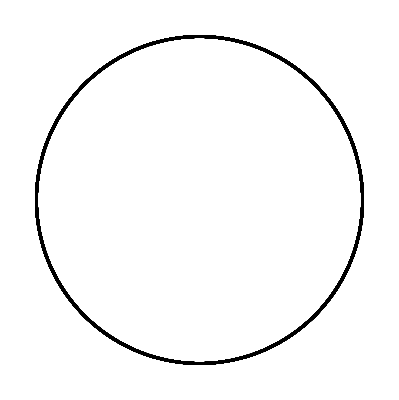

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.%],{t,0,200*Pi},PlotPoints->10000,AspectRatio->Automatic,Axes->False, PlotStyle -> {Black,Thickness[0.005]}]
```

```mathematica
Export["gravity1.eps",%,"EPS",ImageSize->144]
```

gravity1.eps

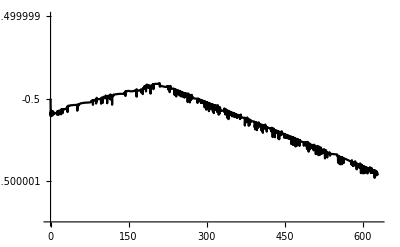

```mathematica
Plot[Evaluate[-1/Sqrt[x[t]^2+y[t]^2]+(x'[t]^2+y'[t]^2)/2 /. %%],{t,0,200*Pi},PlotStyle->{Black},BaseStyle->{FontSize->12},PlotRange->{-0.5000015,-0.499999},Ticks->{Automatic,{-0.500001,-0.5,-0.499999}}]
```

```mathematica
Export["gravity1_err.eps",%,"EPS",ImageSize->300]
```

gravity1_err.eps

```mathematica
Min[Table[Evaluate[-1/Sqrt[x[t]^2+y[t]^2]+(x'[t]^2+y'[t]^2)/2 /. %1],{t,0,200*Pi}]]+0.5
```

-9.69084×10^-7

```mathematica
NDSolve[{x[0]==1,x'[0]==0,y[0]==0,y'[0]==Sqrt[2.],
x''[t]==-x[t]/Sqrt[x[t]^2+y[t]^2]^3,y''[t]==-y[t]/Sqrt[x[t]^2+y[t]^2]^3},
{x,y},{t,0,20},MaxSteps->100000,AccuracyGoal->9]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

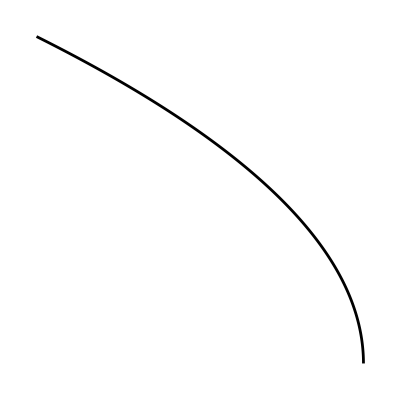

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.%],{t,0,20},PlotPoints->1000,AspectRatio->1,Axes->False,PlotStyle -> {Black,Thickness[0.005]}]
```

```mathematica
Export["gravity2.eps",%,"EPS"]
```

gravity2.eps

```mathematica
NDSolve[{x[0]==1,x'[0]==0,y[0]==0,y'[0]==1.2,
x''[t]==-x[t]/Sqrt[x[t]^2+y[t]^2]^2.9,y''[t]==-y[t]/Sqrt[x[t]^2+y[t]^2]^2.9},
{x,y},{t,0,80*Pi},AccuracyGoal->9];
```

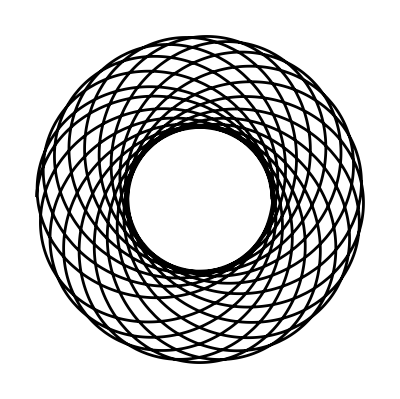

```mathematica
ParametricPlot[{Evaluate[{x[t],y[t]}/.%],{0,0}},{t,0,80*Pi},PlotPoints->200,AspectRatio->Automatic,Axes->False, PlotStyle->{{Black,Thickness[0.005]},{Black}}]
```

```mathematica
Export["gravity3.eps",%,"EPS",ImageSize->144]
```

gravity3.eps

```mathematica
Export["gravity5.gif",%,"GIF"]
```

gravity5.gif

```mathematica
NDSolve[{x1[0]==1.,x1'[0]==0,y1[0]==0,y1'[0]==1,
            x2[0]==1.8,x2'[0]==-1,y2[0]==1.255,y2'[0]==0.001,
x1''[t]==-x1[t]/Sqrt[x1[t]^2+y1[t]^2]^3,
y1''[t]==-y1[t]/Sqrt[x1[t]^2+y1[t]^2]^3,
x2''[t]==-x2[t]/Sqrt[x2[t]^2+y2[t]^2]^3+0.001*(x1[t]-x2[t])/Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2]^3,
y2''[t]==-y2[t]/Sqrt[x2[t]^2+y2[t]^2]^3+0.001*(y1[t]-y2[t])/Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2]^3},
{x1,y1,x2,y2},{t,0,5 Pi},AccuracyGoal->7];
```

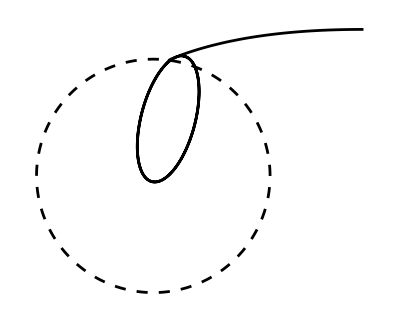

```mathematica
ParametricPlot[{Evaluate[{x2[t],y2[t]}/.%],
                               Evaluate[{x1[t],y1[t]}/. %],{0,0}},{t,0, 2 Pi},AspectRatio->Automatic, Axes->False,    
PlotStyle->{{Black,Thickness[0.005]},
                        {Dashing[{0.02,0.02}],Black,Thickness[0.005]}}]
```

```mathematica
Export["gravity6.eps",%,"EPS", ImageSize->144]
```

gravity6.eps

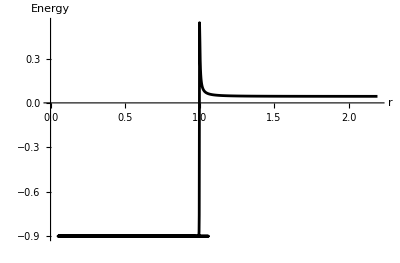

```mathematica
ParametricPlot[Evaluate[{ Sqrt[x2[t]^2+y2[t]^2],-1/Sqrt[x2[t]^2+y2[t]^2]+(x2'[t]^2+y2'[t]^2)/2 } /. %%],{t,0,2Pi},PlotStyle->{Black,Thickness[0.005]},AxesLabel->{"r","Energy"}]
```

```mathematica
Export["gravity6_en.eps",%,"EPS",ImageSize->200]
```

gravity6_en.eps

```mathematica
te = 8Pi;a=3; p=0.1;
```

```mathematica
te=5 Pi;
```

```mathematica
NDSolveValue[{x1[0]==1,x1'[0]==0,y1[0]==0,y1'[0]==1,
            x2[0]==1.8,x2'[0]==-1,y2[0]==1.255,y2'[0]==0.001,
x1''[t]==-x1[t]/Sqrt[x1[t]^2+y1[t]^2]^3,
y1''[t]==-y1[t]/Sqrt[x1[t]^2+y1[t]^2]^3,
x2''[t]==-x2[t]/Sqrt[x2[t]^2+y2[t]^2]^3+0.001*(x1[t]-x2[t])/Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2]^3,
y2''[t]==-y2[t]/Sqrt[x2[t]^2+y2[t]^2]^3+0.001*(y1[t]-y2[t])/Sqrt[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2]^3},
(x2'[te]^2 + y2'[te]^2)/2-1/Sqrt[x2[te]^2+y2[te]^2]-0.001/Sqrt[(x1[te]-x2[te])^2+(y1[te]-y2[te])^2],{t,0,te},AccuracyGoal->8]
```

-0.911894